## Rotational wave-function

-Graphics-

```mathematica
phiM[phi_,M_]:=1/Sqrt[2π] Exp[ⅈ*M*phi*π/180];
```

```mathematica
MLIST[I3_]:=Table[i,{i,-I3,I3,1}];
```

### The nuclear projection along the body-fixed axis

```mathematica
Mval=MLIST[2];
Mval
```

{-2,-1,0,1,2}

### The real part of ψ, for a given set of projections M={-I,...,I}

```mathematica
waveFunction[I_]:=Table[{Table[angle,{i,1,Length[MLIST[I]]}],phiM[angle,MLIST[I]]},{angle,0,180,5}];
```

```mathematica
waveFunction[2]
```

{{{0,0,0,0,0},{1/(√(2 π)),1/(√(2 π)),1/(√(2 π)),1/(√(2 π)),1/(√(2 π))}},{{5,5,5,5,5},{ⅇ^(-(ⅈ π)/18)/(√(2 π)),ⅇ^(-(ⅈ π)/36)/(√(2 π)),1/(√(2 π)),ⅇ^((ⅈ π)/36)/(√(2 π)),ⅇ^((ⅈ π)/18)/(√(2 π))}},{{10,10,10,10,10},{ⅇ^(-(ⅈ π)/9)/(√(2 π)),ⅇ^(-(ⅈ π)/18)/(√(2 π)),1/(√(2 π)),ⅇ^((ⅈ π)/18)/(√(2 π)),ⅇ^((ⅈ π)/9)/(√(2 π))}},{{15,15,15,15,15},{ⅇ^(-(ⅈ π)/6)/(√(2 π)),ⅇ^(-(ⅈ π)/12)/(√(2 π)),1/(√(2 π)),ⅇ^((ⅈ π)/12)/(√(2 π)),ⅇ^((ⅈ π)/6)/(√(2 π))}},{{20,20,20,20,20},{ⅇ^(-(2 ⅈ π)/9)/(√(2 π)),ⅇ^(-(ⅈ π)/9)/(√(2 π)),1/(√(2 π)),ⅇ^((ⅈ π)/9)/(√(2 π)),ⅇ^((2 ⅈ π)/9)/(√(2 π))}},{{25,25,25,25,25},{ⅇ^(-(5 ⅈ π)/18)/(√(2 π)),ⅇ^(-(5 ⅈ π)/36)/(√(2 π)),1/(√(2 π)),ⅇ^((5 ⅈ π)/36)/(√(2 π)),ⅇ^((5 ⅈ π)/18)/(√(2 π))}},{{30,30,30,30,30},{ⅇ^(-(ⅈ π)/3)/(√(2 π)),ⅇ^(-(ⅈ π)/6)/(√(2 π)),1/(√(2 π)),ⅇ^((ⅈ π)/6)/(√(2 π)),ⅇ^((ⅈ π)/3)/(√(2 π))}},{{35,35,35,35,35},{ⅇ^(-(7 ⅈ π)/18)/(√(2 π)),ⅇ^(-(7 ⅈ π)/36)/(√(2 π)),1/(√(2 π)),ⅇ^((7 ⅈ π)/36)/(√(2 π)),ⅇ^((7 ⅈ π)/18)/(√(2 π))}},{{40,40,40,40,40},{ⅇ^(-(4 ⅈ π)/9)/(√(2 π)),ⅇ^(-(2 ⅈ π)/9)/(√(2 π)),1/(√(2 π)),ⅇ^((2 ⅈ π)/9)/(√(2 π)),ⅇ^((4 ⅈ π)/9)/(√(2 π))}},{{45,45,45,45,45},{-ⅈ/(√(2 π)),ⅇ^(-(ⅈ π)/4)/(√(2 π)),1/(√(2 π)),ⅇ^((ⅈ π)/4)/(√(2 π)),ⅈ/(√(2 π))}},{{50,50,50,50,50},{ⅇ^(-(5 ⅈ π)/9)/(√(2 π)),ⅇ^(-(5 ⅈ π)/18)/(√(2 π)),1/(√(2 π)),ⅇ^((5 ⅈ π)/18)/(√(2 π)),ⅇ^((5 ⅈ π)/9)/(√(2 π))}},{{55,55,55,55,55},{ⅇ^(-(11 ⅈ π)/18)/(√(2 π)),ⅇ^(-(11 ⅈ π)/36)/(√(2 π)),1/(√(2 π)),ⅇ^((11 ⅈ π)/36)/(√(2 π)),ⅇ^((11 ⅈ π)/18)/(√(2 π))}},{{60,60,60,60,60},{ⅇ^(-(2 ⅈ π)/3)/(√(2 π)),ⅇ^(-(ⅈ π)/3)/(√(2 π)),1/(√(2 π)),ⅇ^((ⅈ π)/3)/(√(2 π)),ⅇ^((2 ⅈ π)/3)/(√(2 π))}},{{65,65,65,65,65},{ⅇ^(-(13 ⅈ π)/18)/(√(2 π)),ⅇ^(-(13 ⅈ π)/36)/(√(2 π)),1/(√(2 π)),ⅇ^((13 ⅈ π)/36)/(√(2 π)),ⅇ^((13 ⅈ π)/18)/(√(2 π))}},{{70,70,70,70,70},{ⅇ^(-(7 ⅈ π)/9)/(√(2 π)),ⅇ^(-(7 ⅈ π)/18)/(√(2 π)),1/(√(2 π)),ⅇ^((7 ⅈ π)/18)/(√(2 π)),ⅇ^((7 ⅈ π)/9)/(√(2 π))}},{{75,75,75,75,75},{ⅇ^(-(5 ⅈ π)/6)/(√(2 π)),ⅇ^(-(5 ⅈ π)/12)/(√(2 π)),1/(√(2 π)),ⅇ^((5 ⅈ π)/12)/(√(2 π)),ⅇ^((5 ⅈ π)/6)/(√(2 π))}},{{80,80,80,80,80},{ⅇ^(-(8 ⅈ π)/9)/(√(2 π)),ⅇ^(-(4 ⅈ π)/9)/(√(2 π)),1/(√(2 π)),ⅇ^((4 ⅈ π)/9)/(√(2 π)),ⅇ^((8 ⅈ π)/9)/(√(2 π))}},{{85,85,85,85,85},{ⅇ^(-(17 ⅈ π)/18)/(√(2 π)),ⅇ^(-(17 ⅈ π)/36)/(√(2 π)),1/(√(2 π)),ⅇ^((17 ⅈ π)/36)/(√(2 π)),ⅇ^((17 ⅈ π)/18)/(√(2 π))}},{{90,90,90,90,90},{-1/(√(2 π)),-ⅈ/(√(2 π)),1/(√(2 π)),ⅈ/(√(2 π)),-1/(√(2 π))}},{{95,95,95,95,95},{ⅇ^((17 ⅈ π)/18)/(√(2 π)),ⅇ^(-(19 ⅈ π)/36)/(√(2 π)),1/(√(2 π)),ⅇ^((19 ⅈ π)/36)/(√(2 π)),ⅇ^(-(17 ⅈ π)/18)/(√(2 π))}},{{100,100,100,100,100},{ⅇ^((8 ⅈ π)/9)/(√(2 π)),ⅇ^(-(5 ⅈ π)/9)/(√(2 π)),1/(√(2 π)),ⅇ^((5 ⅈ π)/9)/(√(2 π)),ⅇ^(-(8 ⅈ π)/9)/(√(2 π))}},{{105,105,105,105,105},{ⅇ^((5 ⅈ π)/6)/(√(2 π)),ⅇ^(-(7 ⅈ π)/12)/(√(2 π)),1/(√(2 π)),ⅇ^((7 ⅈ π)/12)/(√(2 π)),ⅇ^(-(5 ⅈ π)/6)/(√(2 π))}},{{110,110,110,110,110},{ⅇ^((7 ⅈ π)/9)/(√(2 π)),ⅇ^(-(11 ⅈ π)/18)/(√(2 π)),1/(√(2 π)),ⅇ^((11 ⅈ π)/18)/(√(2 π)),ⅇ^(-(7 ⅈ π)/9)/(√(2 π))}},{{115,115,115,115,115},{ⅇ^((13 ⅈ π)/18)/(√(2 π)),ⅇ^(-(23 ⅈ π)/36)/(√(2 π)),1/(√(2 π)),ⅇ^((23 ⅈ π)/36)/(√(2 π)),ⅇ^(-(13 ⅈ π)/18)/(√(2 π))}},{{120,120,120,120,120},{ⅇ^((2 ⅈ π)/3)/(√(2 π)),ⅇ^(-(2 ⅈ π)/3)/(√(2 π)),1/(√(2 π)),ⅇ^((2 ⅈ π)/3)/(√(2 π)),ⅇ^(-(2 ⅈ π)/3)/(√(2 π))}},{{125,125,125,125,125},{ⅇ^((11 ⅈ π)/18)/(√(2 π)),ⅇ^(-(25 ⅈ π)/36)/(√(2 π)),1/(√(2 π)),ⅇ^((25 ⅈ π)/36)/(√(2 π)),ⅇ^(-(11 ⅈ π)/18)/(√(2 π))}},{{130,130,130,130,130},{ⅇ^((5 ⅈ π)/9)/(√(2 π)),ⅇ^(-(13 ⅈ π)/18)/(√(2 π)),1/(√(2 π)),ⅇ^((13 ⅈ π)/18)/(√(2 π)),ⅇ^(-(5 ⅈ π)/9)/(√(2 π))}},{{135,135,135,135,135},{ⅈ/(√(2 π)),ⅇ^(-(3 ⅈ π)/4)/(√(2 π)),1/(√(2 π)),ⅇ^((3 ⅈ π)/4)/(√(2 π)),-ⅈ/(√(2 π))}},{{140,140,140,140,140},{ⅇ^((4 ⅈ π)/9)/(√(2 π)),ⅇ^(-(7 ⅈ π)/9)/(√(2 π)),1/(√(2 π)),ⅇ^((7 ⅈ π)/9)/(√(2 π)),ⅇ^(-(4 ⅈ π)/9)/(√(2 π))}},{{145,145,145,145,145},{ⅇ^((7 ⅈ π)/18)/(√(2 π)),ⅇ^(-(29 ⅈ π)/36)/(√(2 π)),1/(√(2 π)),ⅇ^((29 ⅈ π)/36)/(√(2 π)),ⅇ^(-(7 ⅈ π)/18)/(√(2 π))}},{{150,150,150,150,150},{ⅇ^((ⅈ π)/3)/(√(2 π)),ⅇ^(-(5 ⅈ π)/6)/(√(2 π)),1/(√(2 π)),ⅇ^((5 ⅈ π)/6)/(√(2 π)),ⅇ^(-(ⅈ π)/3)/(√(2 π))}},{{155,155,155,155,155},{ⅇ^((5 ⅈ π)/18)/(√(2 π)),ⅇ^(-(31 ⅈ π)/36)/(√(2 π)),1/(√(2 π)),ⅇ^((31 ⅈ π)/36)/(√(2 π)),ⅇ^(-(5 ⅈ π)/18)/(√(2 π))}},{{160,160,160,160,160},{ⅇ^((2 ⅈ π)/9)/(√(2 π)),ⅇ^(-(8 ⅈ π)/9)/(√(2 π)),1/(√(2 π)),ⅇ^((8 ⅈ π)/9)/(√(2 π)),ⅇ^(-(2 ⅈ π)/9)/(√(2 π))}},{{165,165,165,165,165},{ⅇ^((ⅈ π)/6)/(√(2 π)),ⅇ^(-(11 ⅈ π)/12)/(√(2 π)),1/(√(2 π)),ⅇ^((11 ⅈ π)/12)/(√(2 π)),ⅇ^(-(ⅈ π)/6)/(√(2 π))}},{{170,170,170,170,170},{ⅇ^((ⅈ π)/9)/(√(2 π)),ⅇ^(-(17 ⅈ π)/18)/(√(2 π)),1/(√(2 π)),ⅇ^((17 ⅈ π)/18)/(√(2 π)),ⅇ^(-(ⅈ π)/9)/(√(2 π))}},{{175,175,175,175,175},{ⅇ^((ⅈ π)/18)/(√(2 π)),ⅇ^(-(35 ⅈ π)/36)/(√(2 π)),1/(√(2 π)),ⅇ^((35 ⅈ π)/36)/(√(2 π)),ⅇ^(-(ⅈ π)/18)/(√(2 π))}},{{180,180,180,180,180},{1/(√(2 π)),-1/(√(2 π)),1/(√(2 π)),-1/(√(2 π)),1/(√(2 π))}}}

```mathematica
wf=waveFunction[1][[1]];
wf
Table[{wf[[i,1]],wf[[i,2]]},{i,1,Length[wf][[1]]}]
```

{{0,0,0},{1/(√(2 π)),1/(√(2 π)),1/(√(2 π))}}

Part::partd: Part specification 2⟦1⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,2⟦1⟧} does not have appropriate bounds.

Table[{wf⟦i,1⟧,wf⟦i,2⟧},{i,1,2⟦1⟧}]

#### Choose rotation/orientation angle (ϕ=20°)

```mathematica
ϕ=20;
```

### Rotational wave-function

```mathematica
Do[Print[m," -> | ",phiM[ϕ,m]," >"],{m,-4,4,1}]
```

-4 -> | ⅇ^(-(4 ⅈ π)/9)/(√(2 π)) >

-3 -> | ⅇ^(-(ⅈ π)/3)/(√(2 π)) >

-2 -> | ⅇ^(-(2 ⅈ π)/9)/(√(2 π)) >

-1 -> | ⅇ^(-(ⅈ π)/9)/(√(2 π)) >

0 -> | 1/(√(2 π)) >

1 -> | ⅇ^((ⅈ π)/9)/(√(2 π)) >

2 -> | ⅇ^((2 ⅈ π)/9)/(√(2 π)) >

3 -> | ⅇ^((ⅈ π)/3)/(√(2 π)) >

4 -> | ⅇ^((4 ⅈ π)/9)/(√(2 π)) >

### Rotational wave - function (real-part)

```mathematica
RephiM[phi_,M_]:=If[Im[phiM[phi,M]]==0,phiM[phi,M],Re[phiM[phi,M]]];
```

```mathematica
RephiM[20,4]
```

Sin[π/18]/(√(2 π))

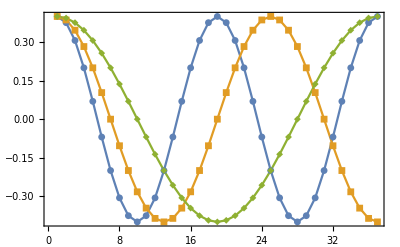

```mathematica
ListPlot[{Table[RephiM[phi,4],{phi,0,180,5}],Table[RephiM[phi,3],{phi,0,180,5}],Table[RephiM[phi,2],{phi,0,180,5}]},Joined->True,Axes->False,PlotMarkers->{Automatic, Small},Frame->True,PlotRange->All]
```

## Plot φ_M(ϕ)

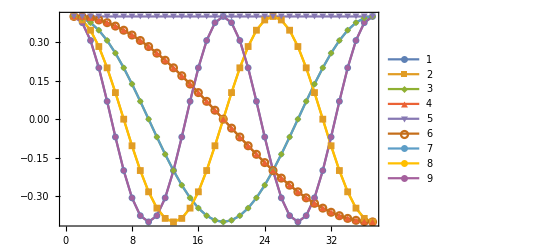

```mathematica
lp[I_]:=ListPlot[Table[Table[RephiM[phi,M],{phi,0,180,5}],{M,-I,I,1}],Joined->True,PlotMarkers->{Automatic, Small},Frame->True,Axes->False,PlotLegends->Automatic];
lp[4]
```

## Plot |Subscript[φ, M](ϕ)|^2

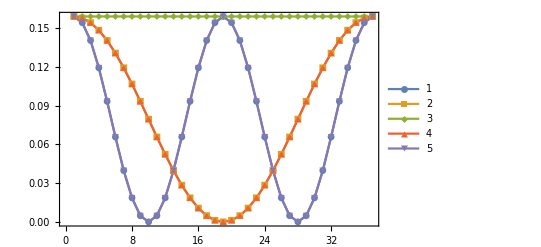

-Graphics-

-Graphics-

```mathematica
lp2[I_]:=ListPlot[Table[Table[Abs[RephiM[phi,M]^2],{phi,0,180,5}],{M,-I,I,1}],Joined->True,PlotMarkers->{Automatic, Small},Frame->True,Axes->False,PlotLegends->Automatic];
lp2[2]
```